```mathematica
SetDirectory[NotebookDirectory[]];
Get["Package.m"];
```

# Rappresentazione Grafica delle Funzioni -Graphics- >< Versione Studente ><

## a cura di

Simone Bertolini, Alessio Francesconi, Matteo Grillini

## 1.1 Introduzione

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

Item duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

Subitem nam liber tempor cum soluta nobis eleifend option congue nihil imperdiet doming id quod mazim placerat facer possim assum.

Subitem typi non habent claritatem insitam; est usus legentis in is qui facit eorum claritatem.

### Equazioni di 1° Grado (Rette)

Teoria

Esercizi

### Equazioni di 2° Grado (Parabole)

Teoria

Esercizi

### Equazioni di 3° Grado

Teoria

Esercizi

Equazioni di 1 °Grado

### Introduzione

Conosciamo la forma delle funzioni di primo grado : f (x) = m X + q ma cosa vogliono dire i parametri m e q?

Ma soprattutto non ti ricorda la forma della retta?

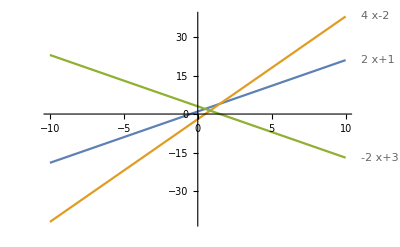

```mathematica
Plot[{2x+1,4x-2,-2x+3}, {x,-10,10},PlotLabels->"Expressions"](* Plotting some functions as example *)
```

### Comprensione guidata del parametro Q

Partiamo cercando di capire cosa rappresenta il q della formula nei grafici :

```mathematica
Manipulate[Plot[2*x+ q ,{x,-3, +3}, PlotRange-> zoom,PlotLabel-> 2x+q],{q, -10,+10},{zoom,10,1000}](* Plotting an example, TODO: Check if zoom function is correct *)
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia q?","Il termine noto q indica l’ordinata del punto di intersezione del grafico con l’asse Y",LinkHand] (* Creating a cliccable text *)
```

Hai dubbi su come cambia il grafico quando cambia q?

### Comprensione del caso particolare

Hai posto attenzione a cosa succede quando q = 0?

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "AG_C1_G1"],{EvaluationNotebook[], "AG_C1_G1"}],"\t",Button["No",If[p1== 0,p1=1;Print[Plot[2x, {x,-5,+5}, PlotLegends->"y = 2 x + 0"]]]]}] (* Generating Button[YES] to proceed and Button[NO] to draw the answer *)
```

No

### Analisi guidata del coefficiente di primo grado

Ora abbiamo capito cosa vuol dire il termine noto sul grafico ma il coefficiente di primo grado m come si traduce sul grafico?

```mathematica
Manipulate[Plot[m*x+-2 ,{x,-3, +3}, PlotRange-> zoom,PlotLabel-> m x-2],{m, -10,+10},{zoom,10,1000}]
```

```mathematica
EventHandler[MouseAppearance[Style["Hai dubbi su come cambia il grafico quando cambia m?” ",FontColor->Blue],LinkHand],{"MouseClicked":>  MessageDialog["Il coefficiente di primo grado indica l’inclinazione del grafico rispetto all’asse X"]}]
```

Hai dubbi su come cambia il grafico quando cambia m?”

### Comprensione del caso particolare

Hai notato cosa cambia se m < 0 o m > 0?

Si	No

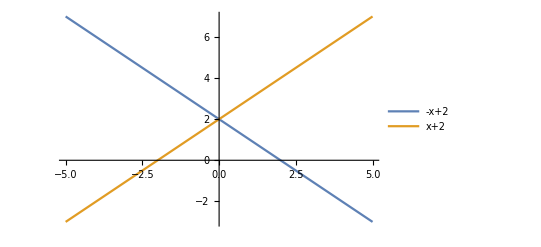

Come puoi vedere i grafici formano con l’asse X angoli acuti se m>0 e ottusi se m<0

```mathematica
Row[{Button["Si"],"\t",Button["No",If[p2 == 0,p2=1;Print[Plot[{-x+2,x+2}, {x,-5,+5}, PlotLegends->"Expressions"]]; Print["Come puoi vedere i grafici formano con l’asse X angoli acuti se m>0 e ottusi se m<0"],p2=1]]}]
```

### Comprensione del caso particolare

Hai notato cosa succede se m = 0?

```mathematica
Row[{Button["Si" ],"\t",Button["No",If[p3 == 0,p3=1;Print[Plot[0x+1, {x,-5,+5}, PlotLegends->"Expressions"]]; Print["Come puoi vedere il grafico è parallelo all'asse X"],p3=1]]}]
```

Si	No

### Caso particolare X=k

Prima di farti sperimentare liberamente bisogna riflettere su un caso unico delle rette non delle funzioni.
Pensa a quale possa essere e poi scopriamolo insieme.


Il caso delle rette verticali che sono della forma X=k con k che è un qualunque numero.

```mathematica
Manipulate[ListLinePlot[{{k,10},{k,-10}},PlotRange->{{-4,+4},{-4,+4}},PlotLabel->StringJoin["x = ",ToString[k]]],{k,-3.5,3.5}]
```

### Ora tocca a te!

Inserisci tu le rette e osserva come sono rappresentate graficamente.Puoi confrontare contemporaneamente 5 equazioni

```mathematica
freeEq = {}(* List that contains at most 5 expressions to be compared, TODO: Insert in package*)
```

{}

```mathematica
currentEq ="" (* Current expression that user is inserting, TODO: Insert in package *)
```

```mathematica
Dynamic[freeEq] (* DEBUG *)
```

```mathematica
Panel[Column[{
Row[{InputField[Dynamic[currentEq],String],Button["Confronta",If[Length[freeEq]<5,AppendTo[freeEq,ToExpression[currentEq]],MessageDialog["Hai già inserito 5 grafici, eliminane uno prima di aggiungerne uno nuovo!"]]]}],Dynamic[Row[Table[With[{i=i},Column[{Plot[freeEq[[i]],{x,-10,+10},PlotLabel->ToString[freeEq[[i]]],ImageSize->Small],"\t",Button["Elimina",freeEq=Delete[freeEq,Position[freeEq,freeEq[[i]]]]]}]],{i,Length[freeEq]}]]]}]](* Drawing the list of the functions that the user want to compare, Delete button allow to remove that expression from the list; TODO Insert in package *)
```

```mathematica
{{"Confronta"}, {}}
```

### Esercizi

```mathematica
teacherEQ = {}; (* Exercises solutions list *)
```

```mathematica
correctAnswer = 0;(* User corrected answer number *)
```

```mathematica
teacherEQ = ReadList["g1.txt"] ;(* Loading teacher's file *)
```

```mathematica
If[Length[teacherEQ===0],teacherEQ= {}]; (* Checking if teacherEQ has been initializated *)
If[Length[teacherEQ]<3,
For[i=0,i<3-Length[teacherEQ],i++,
try = x*RandomInteger[{-10,+10}]+RandomInteger[{-10,+10}];(* Generating new random expression *)
While[ContainsAll[sol,{try}], try = x*RandomInteger[{-10,+10}]+RandomInteger[{-10,+10}]];(* Check that the expression in not already in the solutions lits *)
AppendTo[teacherEQ,try];
]
](* Random function generation: This function complete the excercises list adding Random ones till minimum number is reached *)
```

```mathematica
Dynamic[teacherEQ](* DEBUG *)
```

```mathematica
exercises = {};
For[i=1,i<=Length[teacherEQ],i++,
sol={};
AppendTo[sol,teacherEQ[[i]]];(* Add correct answer *)
coeff = CoefficientList[teacherEQ[[i]],x];(* Get coefficients from expression i *)
 AppendTo[sol,coeff[[1]]-x*coeff[[2]]];(* Add y=-mx+q *)
try = RandomInteger[{-10,10}]+x*RandomInteger[{-10,10}];(* Adding y=RND x + RND *)
While[ContainsAll[sol,{try}], try = RandomInteger[{-10,10}]+x*RandomInteger[{-10,10}]];(* Check that the expression in not already in the solutions lits *)
AppendTo[sol,try];
try = RandomInteger[{-10,10}]+x*coeff[[2]];(* Adding y=mx + RND *)
While[ContainsAll[sol,{try}], try = RandomInteger[{-10,10}]+x*coeff[[2]]];(* Check that the expression in not already in the solutions lits *)
AppendTo[sol,try];
sol=RandomSample[sol]; (* Randomizing the order in the list *)
AppendTo[exercises,sol](* Add exercise to exercises list *)
]
```

```mathematica
Dynamic[exercises](* DEBUG *)
```

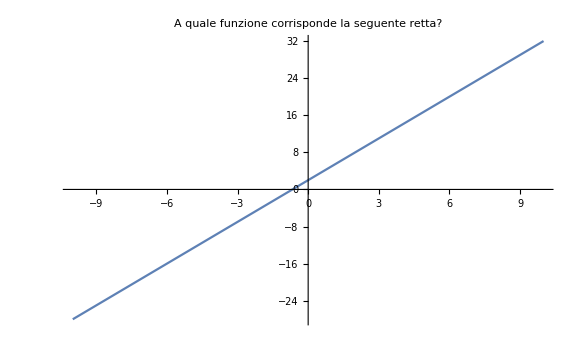
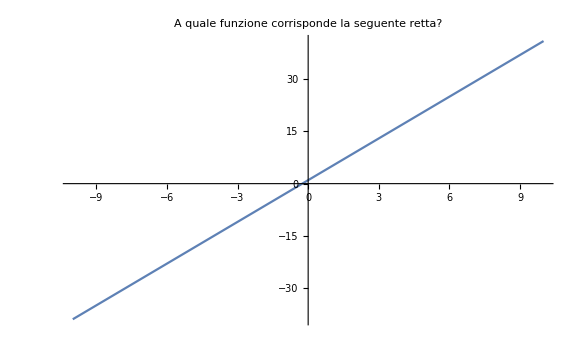
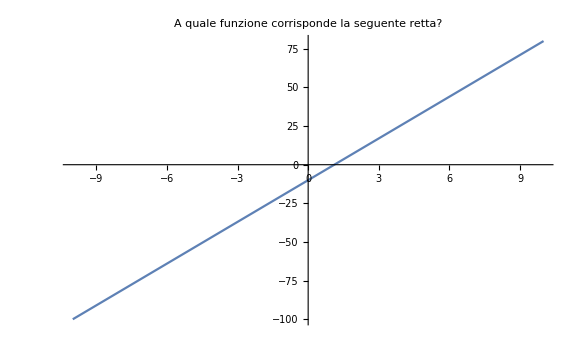
-Graphics-
 | 1+10 x   | 2+3 x   | 5+3 x   | 2-3 x
-Graphics-
 | 5+4 x   | 1+4 x   | 1-4 x   | -5-6 x
-Graphics-
 | -10+9 x   | 7+9 x   | -10-9 x   | -x

```mathematica
s1 = Table[0,Length[teacherEQ]];(* User choises variable *)
en1 = True;(* Form enabling variable *)
Column[Table[With[{i=i},Row[{Panel[Column[{Plot[teacherEQ[[i]],{x,-10,10},ImageSize->Large,PlotLabel->"A quale funzione corrisponde la seguente retta?"],RadioButtonBar[Dynamic[s1[[i]]],exercises[[i]],Enabled->Dynamic[en1]]}]]}
]
],
{i,Length[teacherEQ]}]
]
```

```mathematica
exercises[[1,1]]
```

1+10 x

```mathematica
Length [teacherEQ[[1]]]
```

2

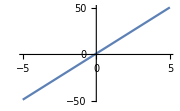
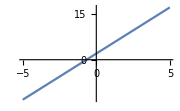
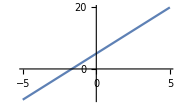
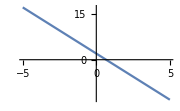
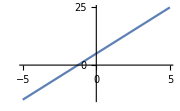
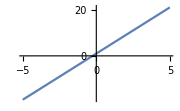
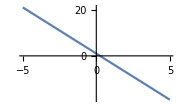
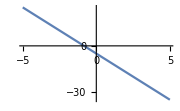
2 + 3 x 	 Qual'è il suo grafico?
-Graphics--Graphics--Graphics--Graphics-
1 + 4 x 	 Qual'è il suo grafico?
-Graphics--Graphics--Graphics--Graphics-
-10 + 9 x 	 Qual'è il suo grafico?
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Column[
Table[
With[{i=i},
Row[{
Panel[
Column[{
Style[StringJoin[ToString[teacherEQ[[i]]]," \t Qual'è il suo grafico?"],FontWeight->Bold],
Row[
Table[
With[{j=j},
Row[{
RadioButton[Dynamic[s1[[i]]],exercises[[i,j]],Enabled->Dynamic[en1]],
Plot[exercises[[i,j]],{x,-5,5},ImageSize-> Small]
}]
],
{j,4}
]
]
}]
]
}]
],
{i,Length[teacherEQ]}
]
]
```

```mathematica
Button["Verifica",
StringAnswer ="";
For[i = 1, i≤ Length[teacherEQ],i++,
If[s1[[i]] === teacherEQ[[i]],
correctAnswer++; 
StringAnswer = StringJoin[StringAnswer,StringJoin[StringJoin["\nEs #",ToString[i]],": Risposta corretta"]];(* 1 is correct *)
 en1 = False; (* Disable retring *),
If[s1[[i]]===0,
StringAnswer=StringJoin[StringJoin["Domanda ",ToString[i]]," non completata"];(* 1 answer has not be given *)
en1 = True; (* Enable retring *) 
Break[],StringAnswer=StringJoin[StringAnswer,StringJoin[StringJoin[StringJoin["\nEs #",ToString[i]],": Risposta errata. Quella corretta era "],ToString[teacherEQ[[i]]]]]; (* 1 error*) 
en1 = False(* Disable retring *)
]
]
];
MessageDialog[StringAnswer](* Output the solution *),
Enabled->Dynamic[en1](* Allowed only 1 click after all answer have been given *)
]1
(* Button that checks if the answer is correct and it blocks user interaction *)
```

Verifica

```mathematica
Dynamic[correctAnswer]/Length[teacherEQ]*100
```

100/3

```mathematica
Dynamic[If[answer===  3,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"E_2G"],{EvaluationNotebook[], "E_2G"}], "Rispondi e Verifica la risposta prima di passare alla prossima sezione"]]
```

Equazioni di 2 °Grado

### Introduzione

```mathematica
Manipulate[Plot[a*x^2+b*x + q ,{x,-3, +3}, PlotRange-> zoom],{a,-10, +10},{b,-10, +10},{q, -10,+10},{zoom,10,1000}]
```

```mathematica
list2 = {}
```

{}

```mathematica
DynamicModule[{f},
Column[
{
Panel[

Row[
{
InputField[
Dynamic[a],Number,FieldSize->Full
],
Style["x^2 + ",12],
InputField[
Dynamic[b],Number,FieldSize->Full
],
Style["x + ",12],
InputField[
Dynamic[q],Number,FieldSize->Full
]
}
]
],
Dynamic@Refresh[f=a*x^2+b*x+ q; "", TrackedSymbols:>{a,b,q}]
Button[
"Add",
If[a== Null ||b== Null || q==Null || a== 0,
MessageDialog["Alcuni campi inseriti non sono corretti!"],
AppendTo[
list2,
f
],
AppendTo[
list2,
f
]
]
] 
}
]
]
```

```mathematica
Dynamic[list2]
```

```mathematica
Dynamic[Plot[list2,{x, -10,10}]]
```

```mathematica
Button[
"Delete",
list2= {}]
```

Delete

Equazioni di 3 °Grado

### Introduzione

```mathematica
Manipulate[Plot[a*x^3+b*x ^2+c*x+ q ,{x,-3, +3}, PlotRange-> zoom],{a,-10, +10},{b,-10, +10},{c,-10,+10},{q, -10,+10},{zoom,10,1000}]
```

```mathematica
list3={}
```

{}

```mathematica
DynamicModule[{f},
Column[
{
Panel[

Row[
{
InputField[
Dynamic[a],Number,FieldSize->Full
],
Style["x^3 + ",12],
InputField[
Dynamic[b],Number,FieldSize->Full
],
Style["x^2 + ",12],
InputField[
Dynamic[c],Number,FieldSize->Full
],
Style["x + ",12],
InputField[
Dynamic[q],Number,FieldSize->Full
]
}
]
],
Dynamic@Refresh[f=a*x^3+b*x^2+c*x + q; "", TrackedSymbols:>{a,b,c,q}]
Button[
"Add",
If[a== Null ||b== Null || c== Null||q==Null || a== 0,
MessageDialog["Alcuni campi inseriti non sono corretti!"],
AppendTo[
list3,
f
],
AppendTo[
list3,
f
]
]
] 
}
]
]
```

```mathematica
Dynamic[list3]
```

```mathematica
Dynamic[Plot[list3,{x,-10, 10}]]
```

```mathematica
Button[
"Delete",
list3= {}]
```

Delete

```mathematica
DialogNotebook[Column[{"The changes have been saved.",DefaultButton[]}]]
```

The changes have been saved.

```mathematica
inputSqrt = "x+1"
```

x+1

```mathematica
Button["√x",
CreateDialog[
Column[
{"Insert Value of Sqrt",InputField[
Dynamic[inputSqrt],String,FieldSize->Full
],DefaultButton[]}
]
]
]
```

√x

```mathematica
Dynamic[inputSqrt]
```

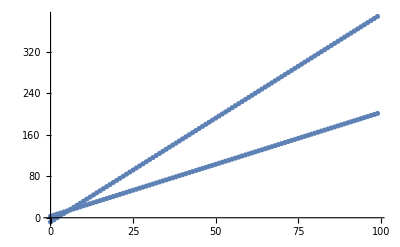

```mathematica
v1={};v2={};
For[t=0,t<100,t=t+1,y=2 t+3;
z=4 t-8;
AppendTo[v1,{t,y}];
AppendTo[v2,{t,z}];]

Show[{ListPlot[v1],ListPlot[v2]},PlotRange->All]
```

```mathematica
Hyperlink[StatusArea["click me","AG_C1_G1"],{EvaluationNotebook[],"AG_C1_G1"}]
```